```mathematica
figNo=1;
captionStyle ={FontFamily-> "Book Antiqua", FontSize->16};
$Line=0;
```

# Chapter 52 | Supporting Notebook Linear Discriminant Analysis Revision 4

## Installing and Checking the IP Package

This installs the IP package, lists and counts the defined functions in IP.m.

```mathematica
Needs["IP`"]
functionListing["IP`"]
functionCount["IP`"]
```

## 51.1 Introduction

No Mathematica code.

## 52.2 Fisher Iris Classification Problem

### 52.2.2 Mathematica code for the ANN

We introduce this discussion by exhibiting the Fisher Iris data, as made available in a WRI-curated dataset.

```mathematica
data = ExampleData[{"Statistics", "FisherIris"}];
Short[data, 3]
```

The option “ColumnDescriptions” retrieves the data column names:

```mathematica
colNames = ExampleData[{"Statistics", "FisherIris"}, "ColumnDescriptions"]
```

Group the data according to the species of iris (GroupBy[] gives an Association[]):

```mathematica
aData = GroupBy[data,Last->Most];
Short[aData, 3]
```

The three keys are:

```mathematica
Keys[aData]
```

Annotations for the parallel axis plot:

```mathematica
frameLabel=Most[colNames]
plotLabel=Last[colNames]
```

$Line=$Line-2;ParallelAxisPlot[ aData,ImageSize->500, AxesLabel->Map[ ToString, Most[colNames]], PlotLabel->ToString[ Last[colNames] ], PlotLegends->Automatic ]//Framed;
(*****)
Labeled[ %,  Style[ StringForm[ "Figure `1`. A ParallelAxisPlot[] showing the four attributes of each of the 150 iris samples.", figNo++],captionStyle] ]//Print

$Line=$Line-2;
framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 58.", 112  ],figNo++], captionStyle ],600 ]

We do not incorporate the following code in this Supporting Notebook; irisnet is redefined later on page 58, and we include that new code.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 58.", 112  ],figNo++], captionStyle ],600 ]

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 58.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
labels = {"setosa", "versicolor", "virginica"}
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 58.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
irisnet = NetInitialize[ NetChain[<|
	"layer1" -> LinearLayer[3],
	"layer2" -> SoftmaxLayer[] |>,
	"Input" -> 4,
	"Output" -> NetDecoder[{"Class", labels}]],
Method -> {"Random", "Weights" -> 1, "Biases" -> 1}]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, pages 58-59.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
Normal@NetExtract[irisnet, {"layer1", "Weights"}] // MatrixForm
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 59.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
Normal@NetExtract[irisnet, {"layer1", "Biases"}]
```

Note that because of different settings of the random number generator in different Notebooks, the actual values produced by the above code will vary from Notebook to Notebook. This is why the numbers above do not correspond to those in DB’s chapter 52.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 59.", 112  ],figNo++], captionStyle ],600 ]

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 59.", 112  ],figNo++], captionStyle ],600 ]

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 60.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
irisnet[{4,5,5,6},"Probabilities"]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 60.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
expDotPlus[input_, weight_, bias_] :=
					Exp[ Dot[weight, input] + bias] /
					Total [Exp[Dot[weight, input] + bias] ]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 60.", 112  ],figNo++], captionStyle ],600 ]

codeInTextCell[ "This gives the same probabilities as the calculation following Figure",figNo-3,"above." ]

```mathematica
expDotPlus[{4, 5, 5, 6},
Normal@NetExtract[irisnet, {"layer1", "Weights"}],
Normal@NetExtract[irisnet, {"layer1", "Biases"}] ]
```

… or more succinctly …

```mathematica
irisnet[{4,5,5,6},"Probabilities"]//Values
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 60.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
(* ⌚ 18-19 secs *)trained = NetTrain[irisnet, {{4, 5, 5, 6} -> "setosa", {3, 2, 4, 3} -> "versicolor", {7, 6, 6, 2} -> "virginica"}]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 60.", 112  ],figNo++], captionStyle ],600 ]

We obtain the same classification with the given input:

```mathematica
trained[ {6,7,7,1}]
```

The associated probabilities are unambiguous:

```mathematica
trained[{6,7,7,1},"Probabilities"]
```

## 52.3 Signal Detection Theory

No Mathematica code.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 62.", 112  ],figNo++], captionStyle ],600 ]

The reference to Exercise 52.6 .6 should be Exercise 52.6 .9.

## 52.4 Personnel Selection

No Mathematica code.

## 52.5 Connections to the Literature

No Mathematica code.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 63.", 112  ],figNo++], captionStyle ],600 ]

In the current version of Mathematica there is no NeuralNetworksClassification[] function as such:

```mathematica
?NeuralNetworksClassification
```

There is, however, a Tech Note, “Classifying Data with Neural Networks”, whose "internal" WDC address is "tutorial/NeuralNetworksClassification". It is opened by the following Button[]:

Print[Style[Button[ "Tech Note: Classifying Data with Neural Networks",NotebookOpen["paclet:/tutorial/NeuralNetworksClassification"](*, Appearance->"Pressed"*)],Background->Magenta]]

Note that in this Tech Note there is an error in the Input cell …

Show[plot, Quiet@Table[ContourPlot[trained[{x, y}, {"Probability", color}] == 0.75, {x, -5, 5}, {y, -5, 5}, ContourStyle -> {Thick, Darker[color, .3]}], {color, {Red, Green, Blue}}]]

… in the clustering  example using samples from three Gaussian distributions. The correct code is …

Show[plot, Quiet@Table[ContourPlot[trained[{x, y}, {"Probabilities", color}] == 0.75, {x, -5, 5}, {y, -5, 5}, ContourStyle -> {Thick, Darker[color, .3]}], {color, {Red, Green, Blue}}]]

codeInTextCell[ "This WDC-based example of an application of neural nets clearly illustrates the nonlinearity of which neural nets are capable. Figure", figNo, "shows:" ]

(i) 600 random samples from each of three bivariate Gaussian distributions with ρ = 0;
(ii) the boundaries of the "95% confidence" regions (specifically, each boundary is the locus of those points at which the classification probability for the nominal class—red, green, blue—is 0.95); and
(iii)  a GrayLevel DensityPlot[] of the Log[] of the classification entropy
-p_red Log[p_red]-p_blue Log[p_blue]-p_green Log[p_green] at each point in -5 ≤ x, y ≤ 5.
The white area indicating the region of highest entropy clearly corresponds to the areas of overlap—and thus classification ambiguity—of the underlying distributions.

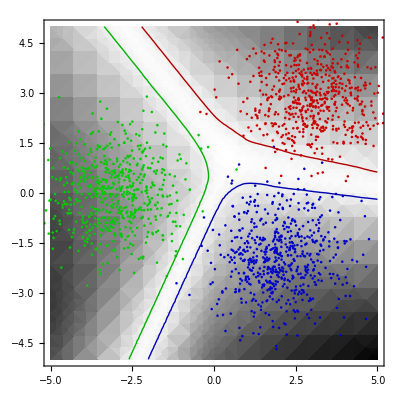
$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "A neural net classification plot.", 112  ],figNo++], captionStyle ],400 ]

DB’s comment on the example in the Tech Note is …

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 63.", 112  ],figNo++], captionStyle ],600 ]

codeInTextCell[ "Figure", figNo, "is the corresponding plot for the bivariate Gaussian example in the Tech Note. Again, the boundaries are boundaries are the respective loci of those points at which the classification probability for the nominal class—red, green, blue—is 0.95. " ]

codeInTextCell[ "The larger (white) area of high entropy than in Figure", figNo-1, "again corresponds to the larger region of overlap of the three distributions." ]

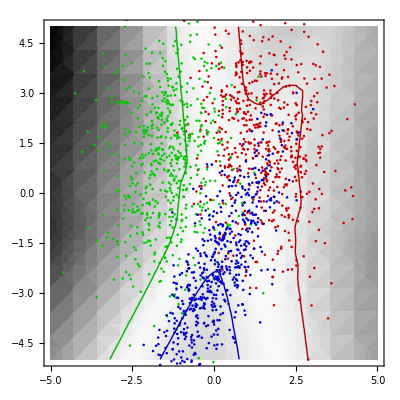
$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Neural net classification plot for the bivariate
Gaussian example in the WDC Tech Note ''Classifying
Data with Neural Networks''.", 500  ],figNo++], captionStyle ],400 ]

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Red, green, and blue probability plots for the bivariate
Gaussian example in the WDC Tech Note ''Classifying
Data with Neural Networks''.", 500  ],figNo++], captionStyle ],550 ]

codeInTextCell[ "Figure",figNo, "shows the results of a neural net classifier applied to an ''egg-in-a-nest'' problem. While it is very clear that the distribution of the red (nest) points cannot possibly be modelled by any bivariate Gaussian distribution, the neural net classifier has been able to determine effective separating boundaries between the red (nest) points and the blue (egg) points." ]

The sharp black-white barrier is due to the fact that at points such as {-4, -4} the entropy value is zero so that the log of the entry is indeterminate. The classification probabilities at {-4,-4} are <|RGBColor[1, 0, 0]→1.,RGBColor[0, 0, 1]→1.24614×10^-18|>.
Near the origin we see that the entropy is very small and log entropy is a negative number (≈ -16)  giving a dark grey level. At {0,0} the classification probabilities are <|RGBColor[1, 0, 0]→3.76227×10^-9,RGBColor[0, 0, 1]→1.|>.
Near {-2.7,0} we see that the entropy is relatively large and log entropy is a small negative number (≈ -0.4) giving a lighter grey level. This is a area of indecision, where the classification probabilities are <|RGBColor[1, 0, 0]→0.466604,RGBColor[0, 0, 1]→0.533396|>.

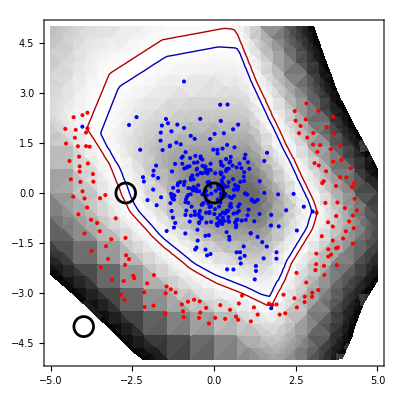
$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Neural net classification plot for an
''egg-within-a-nest'' problem.", 500  ],figNo++], captionStyle ],400 ]

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Neural net classification plot for the bivariate
Gaussian example in the WDC Tech Note ''Classifying
Data with Neural Networks''.", 500  ],figNo++], captionStyle ],550 ]

DB says on page 63:

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 63.", 112  ],figNo++], captionStyle ], captionStyle ],600 ]

In current versions of Mathematica this is not exactly true; it is the only example in Options⟶ValidationSet, where Classify[] is given the option Method -> “LogisticRegression”:

trainingset = ExampleData[{"MachineLearning", "FisherIris"}, "TrainingData"];
c1 = Classify[trainingset, Method -> "LogisticRegression"]

In a second example using the Fisher Iris data, the fifth example in Applications, no option is specified:

Classify[ExampleData[{"MachineLearning", "FisherIris"}, "TrainingData"]]

## 52.6 Solved Exercises for Chapter Fifty Two

### Exercise 52.6.1: Obtain the Fisher Iris data set through Mathematica and then classify a new Iris using a trained network.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 62.", 112  ],figNo++], captionStyle ],600 ]

These are some of the other inputs yielding various attributes of the FisherIris dataset:

ExampleData[{"MachineLearning", "FisherIris"}, "Description"]
ExampleData[{"MachineLearning", "FisherIris"}, "Dimensions"]
ExampleData[{"MachineLearning", "FisherIris"}, "LearningTask"]
ExampleData[{"MachineLearning", "FisherIris"}, "LongDescription"]
ExampleData[{"MachineLearning", "FisherIris"}, "MissingData"]
ExampleData[{"MachineLearning", "FisherIris"}, "Name"]
ExampleData[{"MachineLearning", "FisherIris"}, "Source"]
ExampleData[{"MachineLearning", "FisherIris"}, "VariableDescriptions"]
ExampleData[{"MachineLearning", "FisherIris"}, "VariableTypes"]

Following DB, we assign irisData to the Iris data, and report some of its properties:

```mathematica
irisData = ExampleData[{"MachineLearning", "FisherIris"}, "Data"];
irisData // Length
irisData // Short
Values[irisData] // Tally
Values[irisData] // Union
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 64.", 112  ],figNo++], captionStyle ],600 ]

Note that we give the name trained1 to the network irisnet—defined above—trained on the curated iris data.

```mathematica
(* ⌚ 44-45 secs *)
trained1 = NetTrain[ irisnet, irisData]
```

The (untrained) irisnet and the (trained) trained1 are both NetChains[].

```mathematica
{Head[irisnet],Head[trained1]}
```

```mathematica
trained1[ {6,7,7,1}]
trained1[{6,7,7,1}, "Probabilities"]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 64.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
Values[  irisData]
```

```mathematica
irisnet2 = NetChain[ {LinearLayer[3], SoftmaxLayer[]},
			"Input" -> 4,
			"Output" -> NetDecoder[
						{"Class", Union[Values[irisData]]}] ]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 64.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
(* ⌚ 41-42 secs *)
trained2 = NetTrain[ irisnet2, irisData ]
```

```mathematica
trained2[ {6.1,2.8,4.0,1.3} ]
trained2[{6.1,2.8,4.0,1.3}, "Probabilities"]
```

Recalling from above …

```mathematica
trained1[ {6,7,7,1}]
trained1[{6,7,7,1}, "Probabilities"]
```

… trained2 gives a similar result.

```mathematica
trained2[ {6,7,7,1}]
trained2[{6,7,7,1}, "Probabilities"]
```

A succinct but informative report on a classifier is given by ClassifierMeasurements[]; trained1 and trained2 have virtually identical performance, as seen in their respective confusion matrices.

```mathematica
cm=ClassifierMeasurements[ trained1,irisData]
```

```mathematica
cm=ClassifierMeasurements[ trained2,irisData]
```

Note that the untrained irisnet …

```mathematica
Normal@NetExtract[irisnet,{"layer1","Weights"}]//MatrixForm
Normal@NetExtract[irisnet,{"layer1","Biases"}]
```

… and the trained trained1 …

```mathematica
Normal@NetExtract[trained1,{"layer1","Weights"}]//MatrixForm
Normal@NetExtract[trained1,{"layer1","Biases"}]
```

… have very different weights and biases.

### Exercise 52.6.2: Refresh your memory on how Mathematica represents the univariate Gaussian, or Normal, distribution.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 65.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
PDF[ NormalDistribution[μ,σ], x ]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 65.", 112  ],figNo++], captionStyle ],600 ]

### Exercise 52.6.3: What does attaching a FullForm[] provide?

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, pages 65-66.", 112  ],figNo++], captionStyle ],600 ]

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 66.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
PDF[ NormalDistribution[μ,σ], x ]//FullForm
```

### Exercise 52.6.4: What does attaching TreeForm[] provide?

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 66.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
PDF[ NormalDistribution[μ,σ], x ]//TreeForm
```

### Exercise 52.6.5: Compute the ratio of two Normal distributions with different means but with the same standard deviation.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, pages 67-68.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
PDF [NormalDistribution[Subscript[μ, 1], σ], x] /
			PDF [NormalDistribution[Subscript[μ, 2], σ], x]
```

With specific values for μ_1, μ_2, and σ:

```mathematica
PDF [NormalDistribution[Subscript[μ, 1], σ], x] /
			PDF [NormalDistribution[Subscript[μ, 2], σ], x]/.{Subscript[μ, 1]->0,Subscript[μ, 2]->1,σ->1}
```

This show the ratio of the two Gaussian PDFs—whose equation simplifies to ⅇ^(1/2-x)—with the two Gaussian PDFs.
Note the very different vertical scales possible via the IP package function twoAxisPlot[].

$Line=$Line-2;twoAxisPlot[{PDF[NormalDistribution[μ1, σ], x] / PDF[NormalDistribution[μ2, σ], x],{PDF[NormalDistribution[μ1, σ], x] , PDF[NormalDistribution[μ2, σ], x]}}/.{μ1->0,μ2->1,σ->1},{x,-4,5}, PlotRange->{0,All}];
(*****)
Labeled[ %,  Style[ StringForm[ "Figure `1`. The ratio of two Gaussians (blue) with the two Gaussians (red).", figNo++],captionStyle] ]//Print

### Exercise 52.6.6: Compute the log transform of the ratio of these two Normal distributions and algebraically rework the resulting expression for comparison with a linear discriminant function.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 68.", 112  ],figNo++], captionStyle ],600 ]

We note in passing that sometimes some ingenuity is required in the use of functions such as PowerExpand[], Collect[], Together[], FunctionExpand[], ComplexExpand[], Simplify[], andFullSimplify[] in order to obtain the particular analytic form required. As the WDC says: “Complicated algebraic expressions can usually be written in many different ways. The Wolfram Language provides a variety of functions for converting expressions from one form to another.”

```mathematica
PowerExpand[ Log[ PDF[ NormalDistribution[Subscript[μ, 1], σ], x] /
PDF [NormalDistribution[Subscript[μ, 2], σ], x]]]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 68.", 112  ],figNo++], captionStyle ],600 ]

codeInTextCell[  "Note the transcription errors in the code in the screenshot in figure", figNo-1, "." ]

We think DB transcribed working Mathematica code by hand into the LATEX code that generated the book PDF files, and this process introduced some transcription errors, as here, which RB and BJS failed to notice in their corrections of the original draft of Volume IV.

```mathematica
Equal[
   (* term 1 *) Expand[(x - Subscript[μ, 2])^2 / (2 σ^2) - ((x - Subscript[μ, 1])^2 / (2 σ^2)),
(* term 2*) (x ( Subscript[μ, 1] - Subscript[μ, 2] ) + 1/2 (Subscript[μ, 2]^2 - Subscript[μ, 1]^2)) / σ^2]
]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 68.", 112  ],figNo++], captionStyle ],600 ]

If we apply PowerExpand[] to the ratio of the two Gaussians, as above, then Simplify[] and Collect[] wrt x, we have a linear expression of the form w x + b.
Selecting out the coefficient and constant terms, TraditionalForm[] gives them exactly as given by DB.

codeInTextCell[ "The following code reproduces the terms shown in Figure", figNo-1, "above." ]

```mathematica
Log[ PDF[ NormalDistribution[Subscript[μ, 1], σ], x] /
PDF [NormalDistribution[Subscript[μ, 2], σ], x]]//PowerExpand//Simplify//(s↦Collect[s, x]);
Print[%]
Coefficient[ %%,x, 1]//TraditionalForm//Print
Coefficient[ %%%,x,0]//Simplify//TraditionalForm//Print
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 69.", 112  ],figNo++], captionStyle ],600 ]

### Exercise 52.6.7: Express the univariate Gaussian in a way that makes it easier to match up with the multivariate expression.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 69.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
PDF[NormalDistribution[μ, σ], x]
```

```mathematica
Assuming[  {σ>0}, 1/((2 π)^(1/2)(σ^2)^(1/2))Exp[ -1/2(x-μ)1/σ^2(x-μ) ]//Simplify]
```

```mathematica
%%==%
```

### Exercise 52.6.8: Proceed through the standard Bayesian manipulations for the most primitive of all signal detection scenarios.

No Mathematica code.

### Exercise 52.6.9: As an illustration of my remarks about the one model assigning the probabilities in the SDT scenario, transform the continuous signal strength predictor variable into discrete categories.

No Mathematica code.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 72.", 112  ],figNo++], captionStyle ], captionStyle ],600 ]

codeInTextCell[ "The hidden code producing Figure", figNo-1,"shows how each entry in this table can be calculated." ]

$Line=$Line-3;
TextGrid[
Module[{length,pNoise,pSignal,xInterval,xValue},
  xValue={-Infinity,-2.5,-1.5,-0.5,0.5,1.5,2.5,+Infinity};
  length=Length[xValue];
  
  xInterval=Table[{xValue[[i]],xValue[[i+1]]},{i,length-1}];
  pNoise= Table[Probability[xValue[[i]]<x<xValue[[i+1]],x\[Distributed]NormalDistribution[0,1]],{i,length-1}];
  pSignal=Table[Probability[xValue[[i]]<x<xValue[[i+1]],x\[Distributed]NormalDistribution[1,1]],{i,length-1}];

  Transpose[{xInterval
            ,Round[pNoise/2,0.0001]
            ,Round[pSignal/2,0.0001]
            ,Round[pNoise/2+pSignal/2,0.0001]}
           ]
]
,Frame→All
];
(*****)
Labeled[ %,  Style[ StringForm[ "Figure `1`. The data in
Table 52.1 reproduced.", figNo++],captionStyle] ]//Print

### Exercise 52.6.10: Develop Mathematica code of increasing generality to perform the calculations required in the previous exercise.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 73.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
Integrate[PDF[NormalDistribution[0,1],x],{x,0.5,1.5}]
```

… or …

```mathematica
Probability[0.5<x<1.5,x\[Distributed]NormalDistribution[0,1]]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, pages 73-74.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
Probability[0.5 < x < 1.5,
				Distributed[x, NormalDistribution[1, 1]]]
```

In a more elegant notation …

```mathematica
Probability[0.5<x<1.5,x\[Distributed]NormalDistribution[1,1]]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 74.", 112  ],figNo++], captionStyle ],600 ]

In the more elegant notation …

```mathematica
Probability[-∞ < x < -2.5, x \[Distributed] NormalDistribution[0, 1] ]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 74.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
probver1[{l_, u_}, {mu_, sigma_}] :=
Probability[l < x < u, x \[Distributed] NormalDistribution[mu, sigma] ]
```

```mathematica
probver1[ {-∞,0},{0,1} ]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 74.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
probver2[{l_, u_}, {mu_, sigma_}, dist_] :=
					Probability[l < x < u, x \[Distributed] dist[mu, sigma] ]
```

```mathematica
probver2[ {1,∞},{1,1}, NormalDistribution ]
```

There is a difficulty: how do we specify non-default parameters for the selected distribution? This doesn’t work:

```mathematica
probver2[ {1,∞},{1,1}, NormalDistribution[0,1] ]
```

DB has foreseen the difficulty:

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 74.", 112  ],figNo++], captionStyle ],600 ]

(Note the N[] wrapped around Probability[…] in this definition.)

```mathematica
probver3[{l_, u_}, {params__}, dist_] :=
					N[Probability[l < x < u, x \[Distributed] dist[params]] ]
```

```mathematica
probver3[ {1,∞},{1,1}, NormalDistribution ]
```

We note in passing that it is not good programming practice to employ global free variables in the definition of a function. This illustrates the problem.

```mathematica
x=333;
probver3[ {1,∞},{1,1}, NormalDistribution ]
```

```mathematica
Remove[x]
probver3[ {1,∞},{1,1}, NormalDistribution ]
```

Programming constructs such as Module[] and Block[] allow for local definitions of free variables which are not affected by assignments to Global free variables having the same name outside the function definition. Thus we would prefer …

probver3[{l_, u_}, {params__}, dist_] := Module[ {x},
  					N[Probability[l < x < u, x \[Distributed] dist[params]] ]
  ]

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, pages 74-75.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
probver3[ {-∞,0},{0,1,5}, StudentTDistribution ]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 75.", 112  ],figNo++], captionStyle ],600 ]

### Exercise 52.6.11: Present a few examples from the very wide choice of univariate probability distributions available in Mathematica. Do this in conjunction with the probability function developed in the previous exercise.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 75.", 112  ],figNo++], captionStyle ],600 ]

DB’s reference to “the now renamed prob[]” is puzzling, as prob[] is not used again in Chapter 52. Rather than (invisibly?) rename probver3[] we retain it.

```mathematica
probver3[{-∞, -2.5}, {0, 1}, CauchyDistribution]
probver3[{.5, 1.5}, {1, 1, 1}, WeibullDistribution]
probver3[{.5, 1.5}, {1, 1, 1, 1}, GammaDistribution]
probver3[{0, 20}, {10}, ChiSquareDistribution]
probver3[{0, 15}, {75, -85, 37, 26, 58}, PearsonDistribution]
```

The tiny imaginary component of the Pearson distribution probability suggests why DB defined probver3[] as giving the numerical value of the probability rather than a symbolic expression. The symbolic result for the Pearson distribution probability is a large expression with a LeafCount[] of 184. Simplify[] does not alter the expression at all, while FullSimplify[] spends ≈ 30 seconds reducing the LeafCount[] to 178.

With similar parameter specifications to that of probver3[], probPlot[] illustrates the calculation carried out by probver3[].

```mathematica
probPlot[{1,∞},{1,1},NormalDistribution]
probPlot[{-∞,0},{0,1,5},StudentTDistribution]
probPlot[{-∞,-2.5},{0,1},CauchyDistribution]
probPlot[{0.5,1.5},{1,1,1},WeibullDistribution]
probPlot[{0.5,1.5},{1,1,1,1},GammaDistribution]
probPlot[{0,20},{10},ChiSquareDistribution]
probPlot[{0,15},{75,-85,37,26,58},PearsonDistribution]
```

### Exercise 52.6.12: Approach the joint probability table of Exercise 52.6.9 as if it were to be filled in via the MEP.

No Mathematica code.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 75.", 112  ],figNo++], captionStyle ],600 ]

Here is DB’s Table 52.2:

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 76.", 112  ],figNo++], captionStyle ],600 ]

This introduces an example of what one of us (it’s creator, RB) calls Nemo notation. the symbol A2B7 representing the ordering of the joint statements in a 2×7 statement space, and in effect specifying the largest  (most extreme) index associated with each dimension of the corresponding joint statement table.
According to Wikipedia:
“The oceanic pole of inaccessibility, also known as Point Nemo, is located at roughly 48°52(.6)^`S 123°23(.6)^`W[19] and is the place in the ocean that is farthest from land.”

This reproduces the table in DB’s Table 52.2.

```mathematica
cellTable[A2B7]
```

Here is DB’s Table 52.1:

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 72.", 112  ],figNo++], captionStyle ],600 ]

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 76.", 112  ],figNo++], captionStyle ],600 ]

Assigning 1/14 to each cell …

```mathematica
(* probabilities *)
qi0=Table[1.0,14]/14
```

... gives an entropy of …

```mathematica
(* Entropy *)
Dot[-qi0,Log[qi0]]
```

… which is …

```mathematica
Log[14.0]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 86.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
Round[ArrayReshape[qi0,{2,7}],0.01]
```

```mathematica
cellValue[%]
```

```mathematica
(* Constraint function matrix *) (* Noise | Signal *)
cfm1= {{1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0}};
```

```mathematica
(* Constraint function averages *)
cfa1={1/2};
```

```mathematica
?lagrangeMEP
```

The combination of cfm1 and cfa1 means that the sum of the first seven probabilities is 1/2. This single constraint, given the structure of the problem, is enough to ensure that the maximum entry probabilities are all equal. Effectively, there is no constraint limiting the entropy of the solution, so there is no Lagrange multiplier.

```mathematica
(* Lagrange parameters *)
lagrangeMEP[cfm1,cfa1]
```

The maximum entropy solution is the “flat” or “uninformative” discrete distribution over 14 states …

```mathematica
(* MEP solution Qi values *)
qi1=mepAlgorithmProbabilities[cfm1,cfa1]
%//Rationalize
```

… whose entropy is Log[14]:

```mathematica
(* Entropy *)
Dot[-qi1,Log[qi1]]
Log[14.]
```

We can recover the equivalent number of equally “weighted” alternatives corresponding to this entropy value:

```mathematica
Exp[Dot[-qi1,Log[qi1]]]
```

Next we repeat the previous calculations but with a particular over determined constraint function matrix and constraint function averages. Since these new constraint functions and averages are consistent with the “flat” or “uninformative” discrete distribution over 14 states, we get the same results as before.
(To render the sequence of calculations more compact, we make use of the IP package utility function inputGivesOuput[].)

```mathematica
(* Constraint function matrix *)
```

(cfm2={{1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0} (* Noise | Signal *) 
     ,{1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0} (* interval 1 *) 
     ,{0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0} (* interval 2 *)  
     ,{0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0} (* interval 3 *)  
     ,{0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0} (* interval 4 *)  
     ,{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0} (* interval 5 *)  
     ,{0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0} (* interval 6 *) 
     (*,{0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1} (* interval 7 *) is not required *)
     } )//inputGivesOutput

Dimensions[cfm2]//inputGivesOutput

```mathematica
(* Constraint function averages *)
```

(cfa2={1/2,1/7,1/7,1/7,1/7,1/7,1/7})//inputGivesOutput

```mathematica
(* Lagrange parameters *)
```

lagrangeMEP[cfm2, cfa2]//inputGivesOutput

```mathematica
(* MEP solution Qi values *)
```

(qi2=mepAlgorithmProbabilities[cfm2,cfa2])//inputGivesOutput

(qi2//Rationalize)//inputGivesOutput

```mathematica
(* Entropy *)
```

(Dot[-qi2,Log[qi2]])//inputGivesOutput

Here we repeat the previous calculations but with another over determined constraint function matrix and constraint function averages. Again, since these new constraint functions and averages are also consistent with the “flat” or “uninformative” discrete distribution over 14 states, we get the same results as before.
(Again, to render the sequence of calculations more compact, we make use of the utility function  inputGivesOuput[].)

```mathematica
?inputGivesOutput
```

((* Constraint function matrix *)
cfm2a = {{1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0} (* Noise | Signal *) 
        , {1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0} (* interval 1 *) 
        , {0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0} (* interval 2 *)  
        , {0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0} (* interval 3 *)  
        , {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0} (* interval 4 *)  
        , {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0} (* interval 5 *)  
        , {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0} (* interval 6 *) 
 , {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1} (* interval 7 *) 
        } )//inputGivesOutput

Dimensions[cfm2a]//inputGivesOutput

```mathematica
(* Constraint function averages *)
```

(cfa2 = {1/2, 1/7, 1/7, 1/7, 1/7, 1/7, 1/7, 1/7})//inputGivesOutput

```mathematica
(* Lagrange parameters λ *)
```

lagrangeMEP[cfm2a, cfa2]//inputGivesOutput

```mathematica
(* Rationalised λ values *)
```

Rationalize[ lagrangeMEP[cfm2a, cfa2],1/10^3 ]//inputGivesOutput

```mathematica
(* MEP solution Qi values *)
```

(qi2=mepAlgorithmProbabilities[cfm2a,cfa2])//inputGivesOutput

(qi2//Rationalize)//inputGivesOutput

```mathematica
(* Entropy *)
```

(Dot[-qi2,Log[qi2]])//inputGivesOutput

codeInTextCell[ "Here is code (developed by RB) to generate the 7 discrete probabilities corresponding to the ranges of the unit Gaussian distribution set out in DB's Table 52.1 (our Figure", figNo-3, ") above." ];

```mathematica
Module[{length,pNoise,pSignal,xInterval,xValue},
  xValue={-Infinity,-2.5,-1.5,-0.5,0.5,1.5,2.5,+Infinity};
  length=Length[xValue];
  
  xInterval=Table[{xValue[[i]],xValue[[i+1]]},{i,length-1}];
  pNoise= Table[Probability[xValue[[i]]<x<xValue[[i+1]],x\[Distributed]NormalDistribution[0,1]],{i,length-1}];
  pSignal=Table[Probability[xValue[[i]]<x<xValue[[i+1]],x\[Distributed]NormalDistribution[1,1]],{i,length-1}];

  pNoise/2 + pSignal/2
]
NumberForm[%, {6,4}]
Total[%]
```

The rest of the analysis proceeds as before.

```mathematica
cfa3=Join[{0.5},Most[%%]]  (* 7 constraint function averages *)
```

```mathematica
cfm3=cfm2;  (* same constraint function matrix *)
```

```mathematica
(* Lagrange parameters λ *)
```

```mathematica
lagrangeMEP[cfm3,cfa3]
```

```mathematica
qi3=mepAlgorithmProbabilities[cfm3,cfa3]
```

```mathematica
(* Entropy *)
Dot[-qi3,Log[qi3]]
```

```mathematica
Exp[ Dot[-qi3,Log[qi3]]  ]
```

DB observes that …

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 76.", 112  ],figNo++], captionStyle ],600 ]

and …

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 76-77.", 112  ],figNo++], captionStyle ],600 ]

This constructs the 13x14 constraint function matrix by multiplying the various rows appropriately:

```mathematica
(* Constraint function matrix *)
cfm4={{1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0} (* Noise | Signal *) 
     ,{1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0} (* interval 1 *) 
     ,{0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0} (* interval 2 *)  
     ,{0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0} (* interval 3 *)  
     ,{0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0} (* interval 4 *)  
     ,{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0} (* interval 5 *)  
     ,{0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0} (* interval 6 *) 
     ,{1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0}*{1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0} (* Noise | Signal * interval 1 *)
     ,{1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0}*{0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0} (* Noise | Signal * interval 2 *)
     ,{1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0}*{0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0} (* Noise | Signal * interval 3 *)
     ,{1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0}*{0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0} (* Noise | Signal * interval 4 *)
     ,{1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0}*{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0} (* Noise | Signal * interval 5 *)
     ,{1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0}*{0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0} (* Noise | Signal * interval 6 *)
     };
MatrixForm[cfm4]
Dimensions[cfm4]
```

codeInTextCell[ "This code generates seven Gaussian probabilities for ''Noise''corresponding to the intervals in Figure", figNo-5,"above." ]

```mathematica
Module[{length,pNoise,pSignal,xInterval,xValue},
  xValue={-Infinity,-2.5,-1.5,-0.5,0.5,1.5,2.5,+Infinity};
  length=Length[xValue];
  
  xInterval=Table[{xValue[[i]],xValue[[i+1]]},{i,length-1}];
  pNoise= Table[Probability[xValue[[i]]<x<xValue[[i+1]],x\[Distributed]NormalDistribution[0,1]],{i,length-1}];

  pNoise/2
]
```

We construct the constraint function averages by selecting the 6 relevant ⟨F_i⟩  values and joining them with the previous 7 ⟨F_i⟩  values. The 6 ⟨F_i⟩ values are the first 6 “Noise” values from DB’s Table 52.1 or Table 52.2.

```mathematica
(* Constraint function averages *)
cfa4=Join[cfa3,Most[%]]
```

```mathematica
Length[%]
```

```mathematica
lagrangeMEP[cfm4,cfa4]  (* constraint function matrix *)
```

```mathematica
qi4=mepAlgorithmProbabilities[cfm4,cfa4]
```

```mathematica
(* Entropy *)
Dot[-qi4,Log[qi4]]
```

Recover the equivalent number of equally “weighted” alternatives.

```mathematica
Exp[2.140249890025322]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 77.", 112  ],figNo++], captionStyle ],600 ]

This assigns all the probabilities needed, consistent with the discretized Gaussians 𝒩(0,1) for the “Noise” and 𝒩(1,1) for the “Signal”.

```mathematica
qi5=Module[{length,pNoise,pSignal,xInterval,xValue},
  xValue={-Infinity,-2.5,-1.5,-0.5,0.5,1.5,2.5,+Infinity};
  length=Length[xValue];
  
  xInterval=Table[{xValue[[i]],xValue[[i+1]]},{i,length-1}];
  pNoise= Table[Probability[xValue[[i]]<x<xValue[[i+1]],x\[Distributed]NormalDistribution[0,1]],{i,length-1}];
  pSignal=Table[Probability[xValue[[i]]<x<xValue[[i+1]],x\[Distributed]NormalDistribution[1,1]],{i,length-1}];

  Join[pNoise/2,pSignal/2]
]
```

```mathematica
{Length[qi5],Total[qi5]}
```

The entropy is as above:

```mathematica
(* Entropy *)
{Dot[-qi5,Log[qi5]],Dot[-qi4,Log[qi4]]}
```

codeInTextCell999[ {{"The output from", Text[Style["cellValue[]",FontSize→14]]},{"accords with DB's Figure 52.2 (our Figure", figNo-55},{"):" }}]

```mathematica
Round[ArrayReshape[qi5,{2,7}],0.0001];
cellValue[%]
```

### Exercise 52.6.13: Add some code for computing the metric tensor in the MEP algorithm.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 78.", 112  ],figNo++], captionStyle ],600 ]

codeInTextCell[  "The code in Figure", figNo-1, "cannot be executed in isolation; none of the variables on the right-hand-side have yet been defined." ]

metrictensor = Outer[ D[ Log[zsymbolic], #1, #2] &,
   					lsymbolic, lsymbolic] /. Rest[solution][[1]]

Borrowing code from Appendix A which sets up a problem …

```mathematica
cma = {{1,1,1,1,0,0,0,0},{1,1,0,0,1,1,0,0}};
cfa = {1/2,1/4};
```

… and finds zsymbolic, lsymbolic, and solution …

```mathematica
lsymbolic=Map[Subscript[λ,#]&,Range[Length[cfa]]]
```

```mathematica
zsymbolic=Total[Exp[Dot[lsymbolic,cma]]]
```

```mathematica
solution=NMinimize[Log[zsymbolic]-Dot[lsymbolic,cfa],lsymbolic]
```

```mathematica
codeInTextCell[  "… the code in Figure", figNo-1, "gives a numeric result …" ]
```

```mathematica
metrictensor = Outer[ D[ Log[zsymbolic], #1, #2] &,
   					lsymbolic, lsymbolic] /. Rest[solution][[1]]
```

… that can be rationalised and shown as matrix:

```mathematica
metrictensor//Chop//(s↦Rationalize[s,10^-8])//MatrixForm
```

### Exercise 52.6.14: The logarithmic transform of the multivariate Gaussian distribution also leads to a linear discriminant function. Show this.

No Mathematica code.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 78.", 112  ],figNo++], captionStyle ],600 ]

Because we need to refer to it again, we denote the general bivariate Gaussian PDF by expr1:

```mathematica
expr1=PDF[MultinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{{Subscript[σ, 1]^2,ρ Subscript[σ, 1] Subscript[σ, 2]},{ρ Subscript[σ, 1] Subscript[σ, 2],Subscript[σ, 2]^2}}],{x,y}]
```

We are interested in re-expressing the Log of the PDF; PowerExpand[] is useful here:

```mathematica
expr2=PowerExpand[Log[expr1]]
```

Collect[]-ing and Simplify[]-ing puts expr2 into a more useful form:

```mathematica
expr3 =Collect[expr2,{Subscript[σ, 1]^2,ρ Subscript[σ, 1] Subscript[σ, 2],Subscript[σ, 2]^2},Simplify]
```

We see that the second term in expr3 involves the determinant of the variance-covariance matrix:

```mathematica
det = Det[{{Subscript[σ, 1]^2,ρ Subscript[σ, 1] Subscript[σ, 2]},{ρ Subscript[σ, 1] Subscript[σ, 2],Subscript[σ, 2]^2}} ]//Simplify
```

It is convenient to have a name for the the inverse of the variance-covariance matrix:

```mathematica
sigmaInv = Inverse[{{Subscript[σ, 1]^2,ρ Subscript[σ, 1] Subscript[σ, 2]},{ρ Subscript[σ, 1] Subscript[σ, 2],Subscript[σ, 2]^2}}]//Simplify
```

expr4 is a compact form of (x-μ)^T Σ  (x-μ):

```mathematica
expr4 = (Transpose[{{x-Subscript[μ, 1]}, {y-Subscript[μ, 2]}}]. sigmaInv . {{x-Subscript[μ, 1]}, {y-Subscript[μ, 2]}})⟦1,1⟧//FullSimplify
```

Combining the last three terms in expr3 shows that they differ from expr4 by a factor of -1/2:

```mathematica
(expr3⟦3⟧ + expr3⟦4⟧ + expr3⟦5⟧)
(expr3⟦3⟧ + expr3⟦4⟧ + expr3⟦5⟧)//FullSimplify
```

expr5 combines the separate terms above …

```mathematica
expr5 = -Log[2 π] - 1/2 Log[det] - 1/2 expr4
```

… which is the same as the Log of the PDF in expr3:

```mathematica
expr3 - expr5//Simplify
```

### Exercise 52.6.15: Use Mathematica to explore some beginning numerical relationships about the multivariate Gaussian and from this how a linear discriminant function is formed.

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 79.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
PDF [MultinormalDistribution[{Subscript[μ, 1], Subscript[μ, 2]}, {{1, 0}, {0, 1}}], {x, y}]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, pages 79-80.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
2 π Power[Det[{{1, O}, {0, 1}}], 1/2]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 80.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
Dot [Dot[{x - Subscript[μ, 1], y - Subscript[μ, 2]}, {{1, 0}, {0, 1}}], {x - Subscript[μ, 1], y - Subscript[μ, 2]}]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 80.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
Dot [Dot[{x - Subscript[μ, 1], y - Subscript[μ, 2]}, {{1, 0}, {0, 1}}], {x - Subscript[μ, 1], y - Subscript[μ, 2]}]//Expand
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 80.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
{x - Subscript[μ, 1], y - Subscript[μ, 2]}.({{1, 0}, {0, 1}})
```

```mathematica
{x - Subscript[μ, 1], y - Subscript[μ, 2]}.({{x - Subscript[μ, 1]}, {y - Subscript[μ, 2]}})//Expand
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, pages 80-81.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
Expand[Dot[Dot[{x - Subscript[μ, 1], y - Subscript[μ, 2]}, Inverse[{{σ^2, 0}, {0, σ^2}}]],
											{x - Subscript[μ, 1], y - Subscript[μ, 2]}]]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 81.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
PowerExpand[ Log[ PDF[ MultinormalDistribution[{Subscript[μ, 1], Subscript[μ, 2]},
								{{σ^2, 0}, {0, σ^2}}], {x, y}]]]
```

codeInTextCell[ "If we calculate the two expressions on either side of the == sign in Figure",figNo-1,"(correcting the missing squared numerators on the right-hand side) …" ]

```mathematica
Expand[Dot[Dot[{x - Subscript[μ, 1], y - Subscript[μ, 2]}, Inverse[{{σ^2, 0}, {0, σ^2}}]],
											{x - Subscript[μ, 1], y - Subscript[μ, 2]}]]
 Expand[ 1/2 (-(x-Subscript[μ, 1])^2/σ^2-(y-Subscript[μ, 2])^2/σ^2) ]
```

… we see that the left-hand side is missing a -1/2. Simplifying the logical equality shows the two expressions are equal:

```mathematica
-1/2 Expand[Dot[Dot[{x - Subscript[μ, 1], y - Subscript[μ, 2]}, Inverse[{{σ^2, 0}, {0, σ^2}}]],
											{x - Subscript[μ, 1], y - Subscript[μ, 2]}]] ==
 Expand[ 1/2 (-(x-Subscript[μ, 1])^2/σ^2-(y-Subscript[μ, 2])^2/σ^2) ]//Simplify
```

#### Exercise 52.6.16: Check the plausibility of the above linear discriminant formula with some numbers.

DB finishes his discussion of Exercise 52.6 .25 above with …

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 82.", 112  ],figNo++], captionStyle ],600 ]

This defines a linear discriminant function with this formulation:

```mathematica
ClearAll[linearDiscriminant]
linearDiscriminant[x_List,mean_List,covariance_List,marginal_]:= Dot[Dot[x,Inverse[covariance]],mean]-1/2*Dot[Dot[mean,Inverse[covariance]],mean]+Log[marginal]
```

We can see the general form of the  discriminant function using symbolic input:

```mathematica
linearDiscriminant[{x,y},{Subscript[μ, 1],Subscript[μ, 2]},{{σ^2,0},{0,σ^2}},m]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 83.", 112  ],figNo++], captionStyle ],600 ]

Define the parameters of  the two different groups:

```mathematica
muGroup1={2,4};
muGroup2={-3,-5};
covar={{4,0},{0,4}};
marginalGroup1=3/4;
marginalGroup2=1/4;
```

The observation is …

```mathematica
xPredict={-1,2};
```

These are the two linear discriminant surfaces:

$Line=$Line-2;Plot3D[ linearDiscriminant[{x,y},muGroup1,covar,marginalGroup1], {x, -10,10},{y,-10,10}, PlotRange->All, AxesLabel->{"x","y","ldf"}, ViewPoint->{1.210425045819256,-2.5237,1.90153}]//Framed;
(*****)
Labeled[ %,  Style[ StringForm[ "Figure `1`. The surface described by
linearDiscriminant[{x,y},{2,4},covar,3/4].", figNo++],FontSize→14,FontFamily→"Book Antiqua"] ]//Print

$Line=$Line-2;Plot3D[ linearDiscriminant[{x,y},muGroup2,covar,marginalGroup2], {x, -10,10},{y,-10,10}, PlotRange->All, AxesLabel->{"x","y","ldf"},ViewPoint->{1.210425045819256,-2.5237,1.90153}]//Framed;
(*****)
Labeled[ %,  Style[ StringForm[ "Figure `1`. The surface described by
linearDiscriminant[{x,y},{-3,-5},covar,1/4].", figNo++],FontSize→14,FontFamily→"Book Antiqua"] ]//Print

Shown together, the line of maximum indecision—when the two discriminant functions are equal—must also be linear.

$Line=$Line-2;Show[ {Plot3D[ linearDiscriminant[{x,y},muGroup1,covar,marginalGroup1], {x, -10,10},{y,-10,10}, PlotRange->All, AxesLabel->{"x","y","ldf"}],Plot3D[ linearDiscriminant[{x,y},muGroup2,covar,marginalGroup2], {x, -10,10},{y,-10,10}, PlotRange->All, AxesLabel->{"x","y","ldf"}]},ViewPoint->{1.210425045819256,-2.5237,1.90153} ]//Framed;
(*****)
Labeled[ %,  Style[ StringForm[ "Figure `1`. The intersection of the two planar
surfaces is a straight line.", figNo++],FontSize→14,FontFamily→"Book Antiqua"] ]//Print

The equation of the line on which the two discriminant functions are equal:

```mathematica
solXY = Solve[ {linearDiscriminant[{x,y},muGroup1,covar,marginalGroup1]==linearDiscriminant[{x,y},muGroup2,covar,marginalGroup2]}, {x,y} ]⟦1⟧//Quiet//Simplify
```

In canonical form, this is:

```mathematica
Collect[1/9 (-7-5 x-Log[81])//FullSimplify,x]
```

$Line=$Line-2;Plot[  y/.solXY, {x, -10,10}, AspectRatio->1, ImageSize->350, Frame->True, Axes->False, PlotStyle->Gray,PlotRange->{-10,10},Epilog->{PointSize[0.02],{Red,Point[ muGroup1]},{Purple,Point[ muGroup2]},{Blue,Point[ xPredict]}, {Red,Text["muGroup1", muGroup1-{0,0.75}]},{Purple,Text["muGroup2", muGroup2-{0,0.75}]},{Blue,Text["xPredict", xPredict-{0,0.75}]}} ];
(*****)
Labeled[ %,  Style[ StringForm[ "Figure `1`. The clasification ''boundary'' is
 y = -(5 x)/9+1/9 (-7-4 Log[3]).
The two group means and xPredict are indicated.", figNo++],FontSize→14,FontFamily→"Book Antiqua"] ]//Print

This defines a “binary” classification surface …

```mathematica
classification[  {x_,y_} ]:= If[ y< (y/.solXY),0,1]
```

… that we can also plot:

$Line=$Line-2;Plot3D[ classification[  {x,y} ], {x, -10,10},{y,-10,10},AxesLabel->{"x","y","ldf"}, ViewPoint->{1.93499,-2.38477,1.42079} ]//Framed;
(*****)
Labeled[ %,  Style[ StringForm[ "Figure `1`. classification[{x,y}].", figNo++],FontSize→14,FontFamily→"Book Antiqua"] ]//Print

We first test the linear discriminant function.

At the mean of Group 1 the discriminant function for Group 1 has the value Log[P(Group1 | ℳ_k)]:

```mathematica
linearDiscriminant[muGroup1,muGroup1,covar,marginalGroup1]
Log[marginalGroup1]
```

At the mean of Group 2 the discriminant function for Group 2 has the value Log[P(Group2 | ℳ_k)]:

```mathematica
linearDiscriminant[muGroup2,muGroup2,covar,marginalGroup2]
Log[marginalGroup2]
```

Now we apply the linear discriminant function(s) to the observation xPredict.

```mathematica
lindis1=linearDiscriminant[xPredict,muGroup1,covar,marginalGroup1]
N[%]
```

```mathematica
lindis2=linearDiscriminant[xPredict,muGroup2,covar,marginalGroup2]
N[%]
```

These are the values reported by DB:

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 83.", 112  ],figNo++], captionStyle ],600 ]

Checking on the difference :

```mathematica
lindis1-lindis2//N
```

Here one way to visualise the two distributions and xPredict.

$Line=$Line-3;
Show[
  {Plot3D[{marginalGroup1*PDF[MultinormalDistribution[muGroup1,covar],{x,y}],marginalGroup2*PDF[MultinormalDistribution[muGroup2,covar],{x,y}]}
  ,{x,-10,10},{y,-10,10},PlotRange→All,MeshFunctions→{#3&},MeshShading→{None,Red,None,Yellow},PlotPoints→25, AxesLabel->{"x","y","pdf"}]
  ,
  ListPointPlot3D[{{-1,2,0}},PlotStyle→Directive[PointSize[0.02],Blue]]
  }
]//Framed;
(*****)
Labeled[ %,  Style[ StringForm[ "Figure `1`. The two Gaussian PDFs with xPredict.", figNo++],FontSize→14,FontFamily→"Book Antiqua"] ]//Print

Here is another way ,with the classification boundary shown. Here it is directly computed by ContourPlot[] as the contour of the equality of the two PDFs.

$Line=$Line-3;
Show[
  ContourPlot[marginalGroup1*PDF[MultinormalDistribution[muGroup1,covar],{x,y}],{x,-10,10},{y,-10,10}
  ,Contours→{0.02,0.01,0.005,0.002,0.001,0.0005}
  ,ContourStyle→Red
  ,ContourShading→None
  ,PlotPoints→100
  ,PlotRange→{{-10,10},{-10,10},{0.0,0.03}}
  ]
  ,
  ContourPlot[marginalGroup2*PDF[MultinormalDistribution[muGroup2,covar],{x,y}],{x,-10,10},{y,-10,10}
  ,Contours→{0.02,0.01,0.005,0.002,0.001,0.0005}
  ,ContourStyle→Purple
  ,ContourShading→None
  ,PlotPoints→100
  ,PlotRange→{{-10,10},{-10,10},{0.0,0.03}}
  ]
  ,
  ContourPlot[marginalGroup1*PDF[MultinormalDistribution[muGroup1,covar],{x,y}]==marginalGroup2*PDF[MultinormalDistribution[muGroup2,covar],{x,y}],{x,-10,10},{y,-10,10}
  ,Contours→Automatic
  ,ContourStyle→Gray
  ,ContourShading→None
  ,PlotPoints→100
  ,PlotRange→{{-10,10},{-10,10}}
  ]
  ,
  ListPlot[{Style[{-1,2},Blue],Style[muGroup1,Red],Style[muGroup2,Purple]},PlotStyle→Directive[PointSize[0.02]]],
Epilog->{PointSize[0.02],{Red,Point[ muGroup1]},{Purple,Point[ muGroup2]},{Blue,Point[ xPredict]}, {Red,Text["muGroup1", muGroup1-{0,0.75}]},{Purple,Text["muGroup2", muGroup2-{0,0.75}]},{Blue,Text["xPredict", xPredict-{0,0.75}]}}
];
(*****)
Labeled[ %,  Style[ StringForm[ "Figure `1`. The two Gaussian PDFs with xPredict
and the classification ''boundary'' (obtained as the
contour of equality of the two PDFs).", figNo++],FontSize→14,FontFamily→"Book Antiqua"] ]//Print

The insight that the gray line on this plot provides is that the best linear discriminant is the locus of all points at which the weighted PDFs of the two groups are equal.

The linear discriminant function for classes 1 and 2, as derived by DB, are …

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 83.", 112  ],figNo++], captionStyle ],400 ]

… and …

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 83.", 112  ],figNo++], captionStyle ],400 ]

We define these as follows:

```mathematica
ClearAll[ linearDiscriminant1 ]
linearDiscriminant1[ {x_,y_} ] := (x Subscript[μ, 1] + y Subscript[μ, 2])/σ^2-1/2(Subscript[μ, 1]^2+Subscript[μ, 2]^2)/σ^2 + Log[3/4]/.{Subscript[μ, 1]->2, Subscript[μ, 2]->4, σ->2}//Simplify//(s↦Collect[s,y])
linearDiscriminant1[ {x,y} ]
```

```mathematica
ClearAll[ linearDiscriminant2 ]
linearDiscriminant2[ {x_,y_} ] := (x Subscript[μ, 1] + y Subscript[μ, 2])/σ^2-1/2(Subscript[μ, 1]^2+Subscript[μ, 2]^2)/σ^2 + Log[1/4]/.{Subscript[μ, 1]->-3, Subscript[μ, 2]->-5, σ->2}//Simplify//(s↦Collect[s,y])
linearDiscriminant2[ {x,y} ]
```

What is the equation of the line along which the two discriminant functions are equal? For all points on this line the signal detector or classifier is maximally indecisive.

```mathematica
solLD1LD2 = Solve[ linearDiscriminant1[ {x,y} ]==linearDiscriminant2[ {x,y} ], {y} ]⟦1,1⟧//Simplify//(s↦Collect[s,x])
```

codeInTextCell[ "We've seen this equation above, just before Figure",figNo-7,"." ]

The two linear discriminant functions represent plane surfaces in three dimensions, with their intersection being the line along which the two discriminant functions are equal:

$Line=$Line-2;Plot3D[ {linearDiscriminant1[ {x,y} ], linearDiscriminant2[ {x,y} ]}, {x, -10,10},{y, -10,10} ]//Framed;
(*****)
Labeled[ %,  Style[ StringForm[ "Figure `1`. This looks alot like Figure `2`!.", figNo++,figNo-23],FontSize→14,FontFamily→"Book Antiqua"] ]//Print

codeInTextCell[ "The two discriminant functions evaluated at {-1,2} replicate DB's results, shown in our Figure", figNo-6, "above." ]

```mathematica
linearDiscriminant1[ {-1,2} ]
```

```mathematica
linearDiscriminant2[ {-1,2} ]
```

A plot of these two “probability surfaces” corresponds nicely with the previous plot of the discriminant functions. The red dot is on the probability surface for class 1 and has coordinates {-1, 2,  0.997759}.

$Line=$Line-2;Show[  {Plot3D[ {Exp[ linearDiscriminant1[ {x,y} ] ]/(Exp[ linearDiscriminant1[ {x,y} ] ] + Exp[ linearDiscriminant2[ {x,y} ]]), Exp[ linearDiscriminant2[ {x,y} ] ]/(Exp[ linearDiscriminant1[ {x,y} ] ] + Exp[ linearDiscriminant2[ {x,y} ]])}, {x, -10,10},{y, -10,10}, PlotStyle->{Lighter[Red], Lighter[Purple]}, AxesLabel->{"x","y","posterior
probability"} ],Graphics3D[{Blue,Ellipsoid[{-1,2,Exp[ linearDiscriminant1[ {-1,2} ] ]/(Exp[ linearDiscriminant1[ {-1,2} ] ] + Exp[ linearDiscriminant2[ {-1,2} ]])},{0.25,0.25,0.010}]}]},PlotRange→Full, ImageSize->450];
(*****)
Labeled[ %,  Style[ StringForm[ "Figure `1`. These are the two ''popsterior probability surfaces''
for Group 1 and Group2. xPredict is also indicated.", figNo++,figNo-23],FontSize→14,FontFamily→"Book Antiqua"] ]//Print

(Here is where collapsing a large Figure-generating Input cell makes the Notebook looks so much nicer.)

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 84.", 112  ],figNo++], captionStyle ],600 ]

```mathematica
lpdf[mu1_, mu2_] := PowerExpand[ Log[ PDF[
MultinormalDistribution[{mu1, mu2}, {{σ^2, 0},{0, σ^2}}], {x, y}]
/. {x -> -1, y -> 2, σ -> 2}]]
```

```mathematica
lpdf[Subscript[μ, 1], Subscript[μ, 2]]
```

$Line=$Line-2;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from Chapter 52, page 84.", 112  ],figNo++], captionStyle ],600 ]

We replicate these results:

```mathematica
lpdf[2, 4]
```

```mathematica
lpdf[-3, -5]
```

```mathematica
lpdf[2, 4] - lpdf[-3, -5]
```

Alternately, The posterior probability that the point {-1, 2} belong to class 1 is …

```mathematica
Exp[ linearDiscriminant1[ {-1,2} ] ]/(Exp[ linearDiscriminant1[ {-1,2} ] ] + Exp[ linearDiscriminant2[ {-1,2} ]])//Simplify
```

… whose numerical value is …

```mathematica
%//N
```